## Bh and NoBh Region for (α and Q space time parameters)

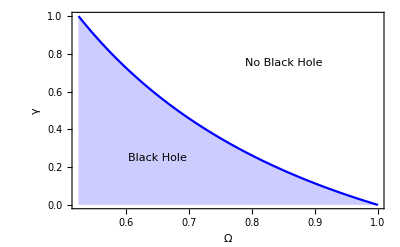

```mathematica
f[r_,Ω_,γ_] = 1-2/r(1+Ω/r^2+(Ω*γ)/r^3)^-1;
gg=Table[γ,{γ,0.,1,0.001}];
OO = Table[Ω/.FindRoot[{(f[r,Ω,γ]/.{γ->gg[[i]]})==0,D[(f[r,Ω,γ]/.{γ->gg[[i]]}),r]==0},{{r,1},{Ω,1}}],{i,1,Length[gg]}];
OOgg = Table[{OO[[i]],gg[[i]]},{i,1,Length[gg]}];

ListLinePlot[OOgg,Frame->True,FrameLabel->{"Ω","γ"},Filling->Axis,LabelStyle->Directive[FontFamily->"Times",FontSize->14,FontColor->Black],PlotRange->{{0.5229,1},{0,1}},PlotStyle->Blue,BaseStyle->{14,FontFamily->"Times"},
Epilog->{Text[Rotate[Framed["Black Hole",FrameStyle->None,Background->None],0Degree],{0.65,0.25}],Text[Rotate[Framed["No Black Hole",FrameStyle->None,Background->None],0Degree],{0.85,0.75}]}]
```

```mathematica
Ω/.FindRoot[{(f[r,Ω,γ]/.{γ->0.5})==0,D[(f[r,Ω,γ]/.{γ->0.5}),r]==0},{{r,1.94},{Ω,1}}]
γ/.FindRoot[{(f[r,Ω,γ]/.{Ω->0.7})==0,D[(f[r,Ω,γ]/.{Ω->0.7}),r]==0},{{r,1.94},{γ,1}}]
(*Ajoyib natijalar*)
```

0.681542

0.457034

## lapse function

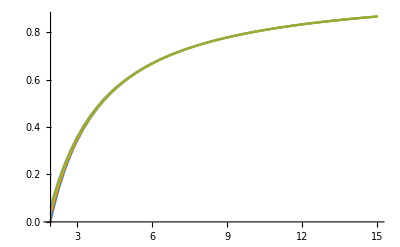

{r→1.93497}

```mathematica
f[r_,Ω_,γ_] = 1-2/r(1+Ω/r^2+(Ω*γ)/r^3)^-1;
Plot[{f[r,0.1,0.5],f[r,0.2,0.5],f[r,0.3,0.5]},{r,1.94,15}]
FindRoot[f[r,0.1,0.5]==0,{r,3}]
```

## Angular momentum and energy

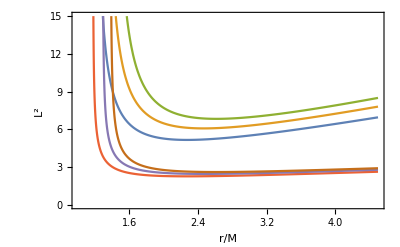

```mathematica
Ene = (-g[r,Q,a,α])/Sqrt[-g[r,Q,a,α] - r^2  *D[g[r,Q,a,α],r]/(2r)];//Simplify
L [r_,Q_,a_,α_]= (r^2 *Sqrt[(-D[g[r,Q,a,α],r])/(2 *r)])/Sqrt[-g[r,Q,a,α] - r^2  *D[g[r,Q,a,α],r]/(2r)];//Simplify

Plot[{L[r,0.3,0.5,-0.1]*L[r,0.3,0.5,-0.1],L[r,0.3,0.5,-0.2]*L[r,0.3,0.5,-0.2],L[r,0.3,0.5,-0.3]*L[r,0.3,0.5,-0.3],L[r,0.3,0.5,-0.1],L[r,0.3,0.5,-0.2],L[r,0.3,0.5,-0.3]},{r,1,4.5},Frame->True,FrameLabel->{"r/M ","L^2"},PlotRange->{{1,4.5},{0,15}}]
```

## Effective Potential

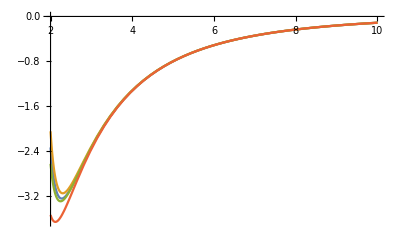

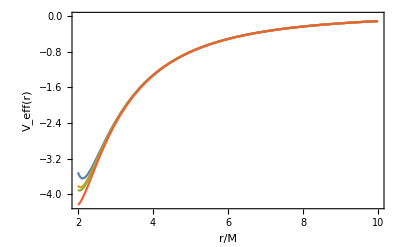

```mathematica
Veff[Ene_,L_,r_,Ω_,γ_]=-1 + Ene^2/f[r,Ω,γ]-L^2/r^2;
Plot[{Veff[1,6,r,0.6,0.],Veff[1,6,r,0.5229,0.2],Veff[1,6,r,0.5229,0.4],Veff[1,6,r,0.5229,0.8]},{r,2,10}]
Plot[{Veff[1,6,r,0.52,0.8],Veff[1,6,r,0.55,0.8],Veff[1,6,r,0.56,0.8],Veff[1,6,r,0.6,0.8]},{r,2,10},FrameLabel->{"r/M","V_eff(r)"},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->14,FontColor->Black]]
```

## ISCO radius